#### Directly from Paper

```mathematica
f1 = 1 - (1-h0)E^(- (vp r / x0)^2)
f =1/(2 π)^(3/2)E^-w f1/.w->1/2(vr^2+vp^2+vesc^2)-ψ 
(*π Integrate[ Integrate[f 2 vp,{vp,0,∞}],{vr,-∞,∞}]-1*)
```

1-ⅇ^(-(r^2 vp^2)/x0^2) (1-h0)

(ⅇ^(1/2 (-vesc^2-vp^2-vr^2)+ψ) (1-ⅇ^(-(r^2 vp^2)/x0^2) (1-h0)))/(2 √2 π^(3/2))

```mathematica
integraloffwrtvp=Integrate[f vp,vp]//Expand
```

-(ⅇ^(-vesc^2/2-vp^2/2-vr^2/2+ψ) r^2)/(√2 π^(3/2) (2 r^2+x0^2))-(ⅇ^(-vesc^2/2-vp^2/2-vr^2/2+ψ) x0^2)/(2 √2 π^(3/2) (2 r^2+x0^2))+(ⅇ^(-vesc^2/2-vp^2/2-vr^2/2-(r^2 vp^2)/x0^2+ψ) x0^2)/(2 √2 π^(3/2) (2 r^2+x0^2))-(ⅇ^(-vesc^2/2-vp^2/2-vr^2/2-(r^2 vp^2)/x0^2+ψ) h0 x0^2)/(2 √2 π^(3/2) (2 r^2+x0^2))

```mathematica
(integraloffwrtvp/.vp->∞)-(integraloffwrtvp/.vp->0)//Simplify
2 π Integrate[ %,{vr,-∞,∞}]//Simplify
```

(ⅇ^(-vesc^2/2-vr^2/2+ψ) (2 r^2+h0 x0^2))/(2 √2 π^(3/2) (2 r^2+x0^2))

(ⅇ^(-vesc^2/2+ψ) (2 r^2+h0 x0^2))/(2 r^2+x0^2)

```mathematica
h[r_]:=(2 r^2+h0 x0^2)/(2 r^2+x0^2)/.h0->1.1/.x0->1
```

```mathematica
1/r D[r ψ[r],{r,2}]==(E^ψ[r] h[r]-1)/.ψ'[r]->0/.r->0
Solve[%,h0]
```

ψ''[0]==-1+ⅇ^ψ[0] h0

{{h0→ⅇ^(-ψ[0]) (1+ψ''[0])}}

```mathematica
D[r ψ[r],{r,2}]==(E^ψ[r] h[r]-1)r//Simplify
```

2 ψ'[r]+r ψ''[r]==r (-1+(ⅇ^ψ[r] (1.1+2 r^2))/(1+2 r^2))

```mathematica
Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]
```

(2 ψ'[r])/r+ψ''[r]

{{ψ→InterpolatingFunction[…]}}

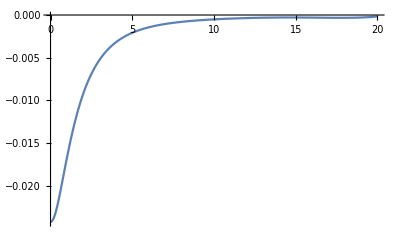

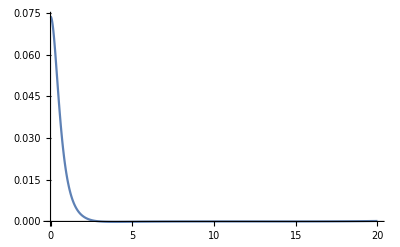

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^ψ[r] (2 r^2+1.1)/(2 r^2+1)-1),ψ[0.001]==-0.0242278902,ψ'[0.001]==0},ψ,{r,0.001,10},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,20},PlotRange->All]
Plot[Laplacian[(ψ/.%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,20},PlotRange->All]
```

{{ψ→InterpolatingFunction[…]}}

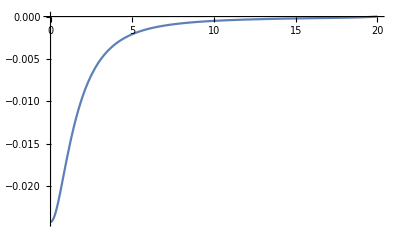

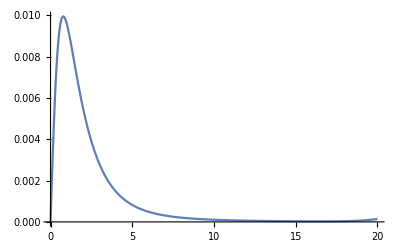

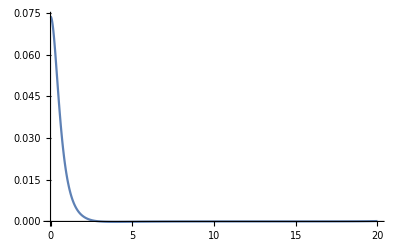

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^ψ[r] (2 r^2+1.1)/(2 r^2+1)-1),ψ[0.001]==-0.0242278892,ψ'[0.001]==0},ψ,{r,0.001,20},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,20},PlotRange->All]
Plot[D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,0.001,20},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,20},PlotRange->All]
```

{{ψ→InterpolatingFunction[…]}}

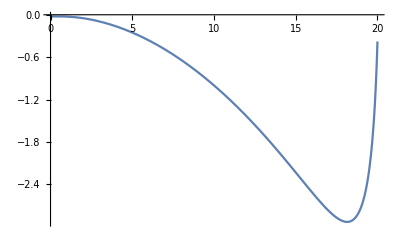

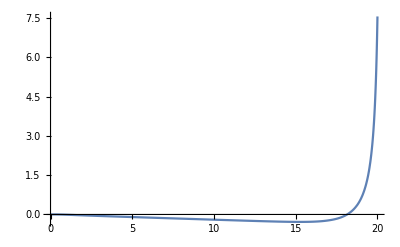

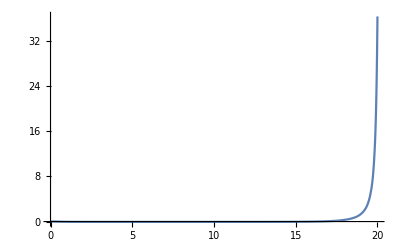

```mathematica
(*NDSolve[{(r Laplacian[ψ[r]+10^-2 r^2,{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(ψ[r]+10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)-1),ψ[0.001]==-0.02422776,ψ'[0.001]==0},ψ,{r,0.001,20},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,20},PlotRange->All]
Plot[D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,0.001,20},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,20},PlotRange->All]*)
```

{{ψ→InterpolatingFunction[…]}}

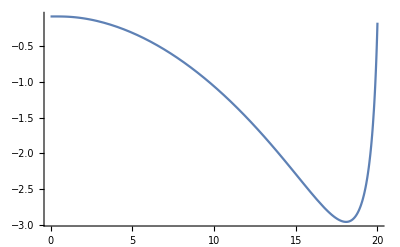

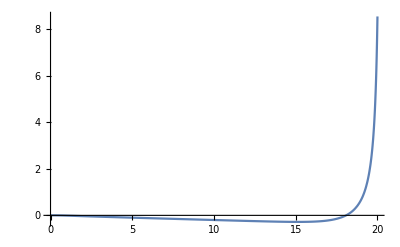

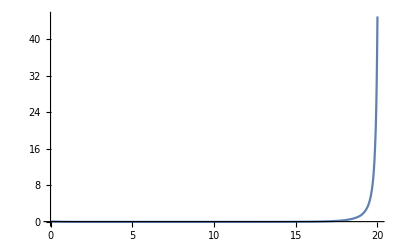

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(ψ[r]+10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)-1),ψ[0.001]==-0.085347,ψ'[0.001]==0},ψ,{r,0.001,20},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,20},PlotRange->All]
Plot[D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,0.001,20},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,20},PlotRange->All]
```

{{ψ→InterpolatingFunction[…]}}

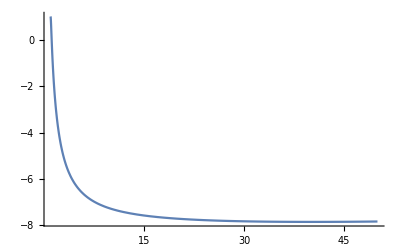

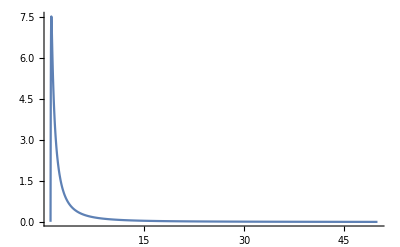

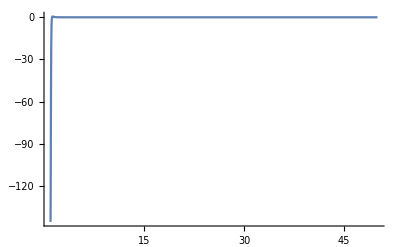

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(ψ[r]+1/r) (2 r^2+1.1)/(2 r^2+1)-E^(3 ψ[r]+2/r) (2 r^2+1.1)/(2 r^2+1)),ψ[1]==1,ψ'[1]==0},ψ,{r,1,50},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,1,50},PlotRange->All]
Plot[-D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,1,50},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,1,50},PlotRange->All]
```

{{ψ→InterpolatingFunction[…]}}

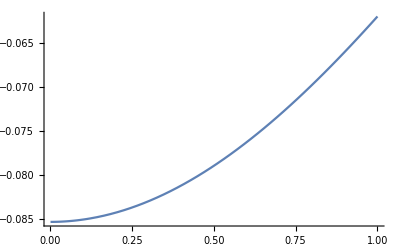

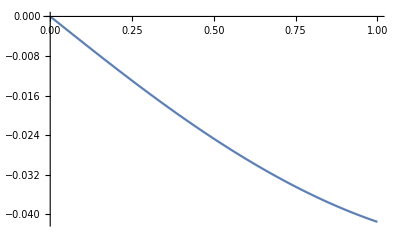

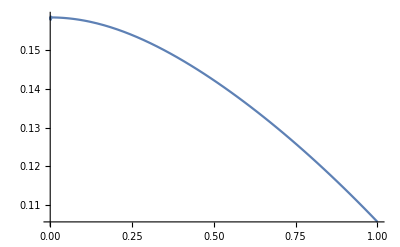

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(ψ[r]+10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)-E^(3ψ[r]+2 10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)),ψ[0.001]==-0.085347,ψ'[0.001]==0},ψ,{r,0.001,1},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,1},PlotRange->All]
Plot[-D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,0.001,1},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,1},PlotRange->All]
```

```mathematica
(*FrontEndExecute[FrontEndToken["Save"]]*)
```

w grav 2 component in the earth

{{ψ→InterpolatingFunction[…]}}

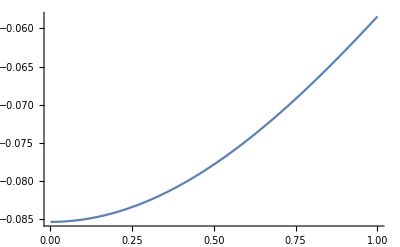

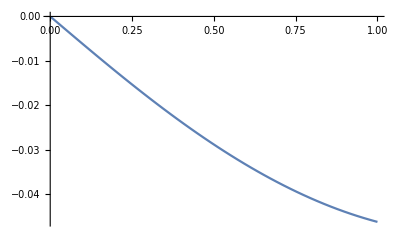

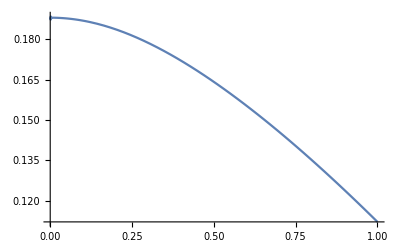

```mathematica
inearthsol=NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(-ψ[r]+10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)-E^(ψ[r]+2 10^-2 r^2) (2 r^2+1.1)/(2 r^2+1)),ψ[0.001]==-0.085347,ψ'[0.001]==0},ψ,{r,0.001,1},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,0.001,1},PlotRange->All]
Plot[-D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,0.001,1},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,0.001,1},PlotRange->All]
```

```mathematica
ψprE=D[(ψ/.inearthsol[[1]])[r],r]/.r->1
ψrE=(ψ/.inearthsol[[1]])[r]/.r->1
```

0.0463027

-0.0584352

w grav 2 component out of the earth

{{ψ→InterpolatingFunction[…]}}

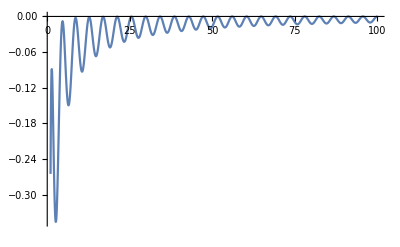

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(E^(-ψ[r]+1/r) (2 r^2+1.1)/(2 r^2+1)-E^(ψ[r]+2/r) (2 r^2+1.1)/(2 r^2+1)),ψ[100]==0,ψ'[100]==0},ψ,{r,1,100},Method->"StiffnessSwitching"]
Plot[(ψ/.%[[1]])[r],{r,1,100},PlotRange->All]
(*Plot[-D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,1,50},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,1,50},PlotRange->All]*)
```

{{ψ→InterpolatingFunction[…]}}

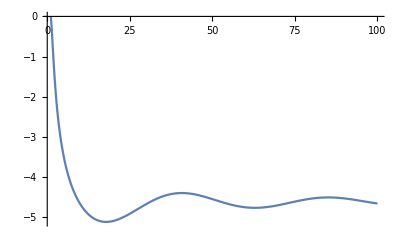

```mathematica
NDSolve[{(r Laplacian[ψ[r],{r,θ,ϕ},"Spherical"]//Simplify)==r(1/10000 E^(-ψ[r]+1/r) (2 r^2+1.1/4)/(2 r^2+1/4)-E^(ψ[r]+2/r) (2 r^2+1.1)/(2 r^2+1)),ψ[1]==-0.001,ψ'[1]==0.01},ψ,{r,1,100}]
Plot[(ψ/.%[[1]])[r],{r,1,100},PlotRange->All]
(*Plot[-D[(ψ/.%%[[1]])[rt],rt]/.rt->r,{r,1,50},PlotRange->All]
Plot[Laplacian[(ψ/.%%%[[1]])[rt],{rt,θ,ϕ},"Spherical"]/.rt->r,{r,1,50},PlotRange->All]*)
```

#### Rmax

```mathematica
vesc2sol=DSolve[r D[vesc2[r],r]+2 (vinf2 + vesc2[r])==0,vesc2[r],r]
Solve[(vesc2[r]/.%[[1]])==vesc2[r],r]
```

{{vesc2[r]→-vinf2+C[1]/r^2}}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-vinf2+C[1]/r^2==vesc2[r],r]

```mathematica
ϕ=2/m vesc2[r]/.vesc2sol[[1]]
```

(2 (-vinf2+C[1]/r^2))/m

```mathematica
ϕ
```

(2 (-vinf2+C[1]/r^2))/m

```mathematica
Solve[D[-q ϕe[r]+1/2 L^2/(m r^2),r]==0,r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-L^2/(m r^3)-q ϕe'[r]==0,r]